# System of linear equations

```mathematica
Remove["Global`*"];
```

## Solve 1

```mathematica
eqns={x+y==4,2x-y==-1};
```

```mathematica
eqns//TableForm
```

x+y==4
2 x-y==-1

```mathematica
Solve[eqns,{x,y}]
```

{{x→1,y→3}}

## Solve 2

```mathematica
m={{1,1},{2,-1}};
```

```mathematica
b={4,-1};
```

```mathematica
LinearSolve[m,b]
```

{1,3}

## Solve 3

```mathematica
m={{1,1},{2,-1}};
```

```mathematica
b={4,-1};
```

```mathematica
eqns=Thread[m.{x,y}==b];
```

```mathematica
eqns//TableForm
```

x+y==4
2 x-y==-1

```mathematica
Solve[eqns,{x,y}]
```

{{x→1,y→3}}

## Solve 4

```mathematica
m//MatrixForm
```

(1 | 1
2 | -1)

```mathematica
b//MatrixForm
```

(4
-1)

```mathematica
a=Transpose[Join[Transpose[m], {b}]];
```

```mathematica
a//MatrixForm
```

(1 | 1 | 4
2 | -1 | -1)

```mathematica
r =RowReduce[a];
```

```mathematica
r//MatrixForm
```

(1 | 0 | 1
0 | 1 | 3)

```mathematica
sol= r[[All,-1]]//MatrixForm
```

(1
3)

## Display the solution

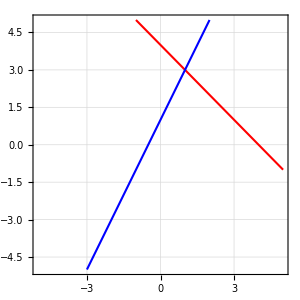

```mathematica
ContourPlot[
{x+y==4,2x-y==-1},
{x,-5,5},{y,-5,5},
ContourStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},
GridLines->Automatic,
GridLinesStyle->Dashed
]
```

## Underdetermined system

```mathematica
m={{1,2,3},{4,5,6}};
```

```mathematica
b={6,15};
```

```mathematica
eqns=Thread[m.{x,y,z}==b];
```

```mathematica
eqns//TableForm
```

x+2 y+3 z==6
4 x+5 y+6 z==15

```mathematica
Solve[eqns,{x,y}]
```

{{x→z,y→3-2 z}}